```mathematica
freqList={309.28, 403.96, 468.56,647.07,679.85,8.14.31, 840.42,937.85,939.83, 943.95}*10^-6;
lList={2,1,3,4,2,0,5,2,3,1};
nList={0,2,0,0,1,0,0,2,1,3};
qList=1000/{1.962,2.52,2.395,2.680,3.222,0.188, 2.812,10.432,3.537,1.209};
```

```mathematica
M=5.972*10^24; 
ρ=5515;
α= 10^4;
β = 10^4;
c=3*10^8;
h=6.6*10^-34/2/Pi;
R=6371*10^3;
u=7.6*10^-8;
p=10^-3*ω/(2 Pi c);
q=ω/α;
```

```mathematica
D[SphericalBesselJ[0,z],z]/.{z->q r};
NIntegrate[Conjugate[%]*%r^2,{r,0,R}];
cn=Sqrt[M/(4Pi%*ρ)];
```

NIntegrate::inumr: The integrand r^2 Conjugate[-(5000 SphericalBesselJ[0,(r ω)/10000])/(r ω)+1/2 (SphericalBesselJ[-1,(r ω)/10000]-SphericalBesselJ[1,Times[«3»]])] (-(5000 SphericalBesselJ[0,(r ω)/10000])/(r ω)+1/2 (SphericalBesselJ[-1,(r ω)/10000]-SphericalBesselJ[1,(r ω)/10000])) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6371000}}.

```mathematica
D[SphericalBesselJ[0,z],z]/.{z->q r};
int=NIntegrate[%*SphericalBesselJ[1,p r]r^2,{r,0,R}]
f=Sqrt[3]M u/( Q(4Pi)cn%SphericalHarmonicY[1,0,0,0])
```

-1.20197×10^10

-8.17332×10^-19

```mathematica
l>0
```

False

```mathematica
Clear[lMode]
Clear[ω]
Clear[Q]
```

```mathematica
M=5.972*10^24; 
ρ=5515;
α= 10^4;
β = 10^4;
c=3*10^8;
h=6.6*10^-34/2/Pi;
R=6371*10^3;
u=7.6*10^-8;
ωSpec=2*Pi*Range[200,1000,0.1]*10^-6;
spec={};
For[index=1,index≤Length[ωSpec], index++,
intList={};
For[modeIndex=1,modeIndex≤Length[lList], modeIndex++,
lMode=lList[[modeIndex]];
ωMode=2*Pi*freqList[[modeIndex]];
Q=qList[[modeIndex]];
lRange=10;
aAngularInt=Table[Integrate[SphericalHarmonicY[lMode,0,θ,ϕ]*Conjugate[SphericalHarmonicY[l,0,θ,ϕ]]*Cos[θ]*Sin[θ],{θ,0,Pi},{ϕ,0,2*Pi}],{l,0,lRange}];
bAngularInt=Table[Integrate[D[SphericalHarmonicY[lMode,0,θ,ϕ],θ]*Conjugate[SphericalHarmonicY[l,0,θ,ϕ]]*Sin[θ]*Sin[θ],{θ,0,Pi},{ϕ,0,2*Pi}],{l,0,lRange}];
p=10^-3*ωSpec[[index]]/(2 Pi c);
q=ωMode/α;
k=ωMode/β;
alpha=0.5*((D[D[SphericalBesselJ[lMode,z],z],z]/.{z->k R})+(lMode-1)(lMode+2)(SphericalBesselJ[lMode,z]/.{z->k R})/(k R)^2);
beta=N[q/k D[SphericalBesselJ[lMode,z]/z,z]/.{z->q R}];
a=alpha*(D[SphericalBesselJ[lMode,z],z]/.{z->q r})-beta*lMode*(lMode+1)SphericalBesselJ[lMode,k r]/(k r);
b=r/R(alpha*SphericalBesselJ[lMode,q r]/(q r)-beta (SphericalBesselJ[lMode,k r]/(k r)+D[SphericalBesselJ[lMode,z],z]/.{z->k r}));
cn=Sqrt[M/ρ /NIntegrate[(a^2*Conjugate[SphericalHarmonicY[lMode,0,θ,ϕ]]*SphericalHarmonicY[lMode,0,θ,ϕ]
+b^2 R^2 (1/r^2 Conjugate[D[SphericalHarmonicY[lMode,0,θ,ϕ],θ]]*D[SphericalHarmonicY[lMode,0,θ,ϕ],θ]+
1/r^2 /Sin[θ]^2Conjugate[D[SphericalHarmonicY[lMode,0,θ,ϕ],ϕ]]*D[SphericalHarmonicY[lMode,0,θ,ϕ],ϕ]))
r^2 Sin[θ],{r,0,R},{θ,0,Pi},{ϕ,0,2*Pi}]];
int=NIntegrate[(aAngularInt*a*Table[I^lBes SphericalHarmonicY[lBes,0,0,0] SphericalBesselJ[lBes,p r],{lBes,0,lRange}]+R*bAngularInt*b*Table[I^lBes SphericalHarmonicY[lBes,0,0,0]SphericalBesselJ[lBes,p r],{lBes,0,lRange}])r^2,{r,0,R}];
intList=Append[intList,cn Total[int]];
];
spec=Append[spec,M*u/Total[(4 Pi I intList)/(4*Pi^2*freqList^2-ωSpec[[index]]^2+I*ωSpec[[index]]*2*Pi*freqList/qList)]];
]
intList
```

Thread::tdlen: Objects of unequal length in {} {455136.-992.486 ⅈ,205630.-339.861 ⅈ,141078.-176.351 ⅈ,66887.5-61.2585 ⅈ,59996.5-62.2558 ⅈ,-633358.-1.50256 ⅈ,38016.-26.9671 ⅈ,30170.7-70.3174 ⅈ,30037.8-23.6816 ⅈ,29763.9-7.98259 ⅈ} cannot be combined.

Total::tllen: Lists of unequal length in {} {455136.-992.486 ⅈ,205630.-339.861 ⅈ,141078.-176.351 ⅈ,66887.5-61.2585 ⅈ,59996.5-62.2558 ⅈ,-633358.-1.50256 ⅈ,38016.-26.9671 ⅈ,30170.7-70.3174 ⅈ,30037.8-23.6816 ⅈ,29763.9-7.98259 ⅈ} cannot be added.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

Set::write: Tag Times in Null {} is Protected.

Thread::tdlen: Objects of unequal length in {6.74986×10^18+0. ⅈ,0.-1.54768×10^27 ⅈ,0.+5.60799×10^9 ⅈ,-3.38217+0. ⅈ,5.15137×10^18+0. ⅈ,-1.18772×10^12+0. ⅈ,0.-1.60278×10^-9 ⅈ,1.23994×10^18+0. ⅈ,0.+5.59529×10^9 ⅈ,0.+8.76841×10^26 ⅈ,6.75323×10^18+0. ⅈ,0.-1.54768×10^27 ⅈ,0.+5.6136×10^9 ⅈ,-3.38724+0. ⅈ,5.15395×10^18+0. ⅈ,-1.18831×10^12+0. ⅈ,0.-1.60599×10^-9 ⅈ,1.24056×10^18+0. ⅈ,0.+5.60089×10^9 ⅈ,0.+8.76841×10^26 ⅈ} {455791.-996.342 ⅈ,205763.-340.644 ⅈ,141140.-176.684 ⅈ,«5»,30040.6-23.7097 ⅈ,29766.7-7.99208 ⅈ} cannot be combined.

Total::tllen: Lists of unequal length in {455791.-996.342 ⅈ,205763.-340.644 ⅈ,141140.-176.684 ⅈ,66901.7-61.3457 ⅈ,60007.8-62.3417 ⅈ,-632093.-1.49806 ⅈ,38020.6-27.0006 ⅈ,30173.5-70.4011 ⅈ,30040.6-23.7097 ⅈ,29766.7-7.99208 ⅈ} {6.74986×10^18+0. ⅈ,0.-1.54768×10^27 ⅈ,0.+5.60799×10^9 ⅈ,-3.38217+0. ⅈ,5.15137×10^18+0. ⅈ,-1.18772×10^12+0. ⅈ,0.-1.60278×10^-9 ⅈ,«6»,-3.38724+0. ⅈ,5.15395×10^18+0. ⅈ,-1.18831×10^12+0. ⅈ,0.-1.60599×10^-9 ⅈ,1.24056×10^18+0. ⅈ,0.+5.60089×10^9 ⅈ,0.+8.76841×10^26 ⅈ} cannot be added.

Set::write: Tag Times in Null {} is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {6.74986×10^18+0. ⅈ,0.-1.54768×10^27 ⅈ,0.+5.60799×10^9 ⅈ,-3.38217+0. ⅈ,5.15137×10^18+0. ⅈ,-1.18772×10^12+0. ⅈ,0.-1.60278×10^-9 ⅈ,1.23994×10^18+0. ⅈ,0.+5.59529×10^9 ⅈ,0.+8.76841×10^26 ⅈ,6.75323×10^18+0. ⅈ,0.-1.54768×10^27 ⅈ,0.+5.6136×10^9 ⅈ,-3.38724+0. ⅈ,«22»+«1»,«1»,0.-1.60599×10^-9 ⅈ,1.24056×10^18+0. ⅈ,0.+5.60089×10^9 ⅈ,0.+8.76841×10^26 ⅈ,6.75661×10^18+0. ⅈ,0.-1.54768×10^27 ⅈ,0.+5.61921×10^9 ⅈ,-3.39232+0. ⅈ,5.15652×10^18+0. ⅈ,-1.18891×10^12+0. ⅈ,0.-1.6092×10^-9 ⅈ,1.24118×10^18+0. ⅈ,0.+5.60649×10^9 ⅈ,0.+8.76841×10^26 ⅈ} «1» cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Total::tllen: Lists of unequal length in {456120.-998.278 ⅈ,205830.-341.036 ⅈ,141172.-176.852 ⅈ,66908.7-61.3893 ⅈ,60013.5-62.3847 ⅈ,-631462.-1.49582 ⅈ,38022.9-27.0173 ⅈ,30175.-70.443 ⅈ,30042.1-23.7238 ⅈ,29768.1-7.99682 ⅈ} {6.74986×10^18+0. ⅈ,0.-1.54768×10^27 ⅈ,0.+5.60799×10^9 ⅈ,-3.38217+0. ⅈ,5.15137×10^18+0. ⅈ,-1.18772×10^12+0. ⅈ,0.-1.60278×10^-9 ⅈ,«16»,-3.39232+0. ⅈ,5.15652×10^18+0. ⅈ,-1.18891×10^12+0. ⅈ,0.-1.6092×10^-9 ⅈ,1.24118×10^18+0. ⅈ,0.+5.60649×10^9 ⅈ,0.+8.76841×10^26 ⅈ} cannot be added.

General::stop: Further output of Total::tllen will be suppressed during this calculation.

Part::partw: Part 11 of {509.684,396.825,417.537,373.134,310.366,5319.15,355.619,95.8589,282.725,827.13} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
ωSpec=2*Pi*Range[200,1000,0.1]*10^-6;
spec={};
For[index=1,index≤Length[ωSpec], index++,
spec=Append[spec,M*u/Total[(4 Pi I intList)/(4*Pi^2*freqList^2-ωSpec[[index]]^2+I*ωSpec[[index]]*2*Pi*freqList/qList)]]
]
```

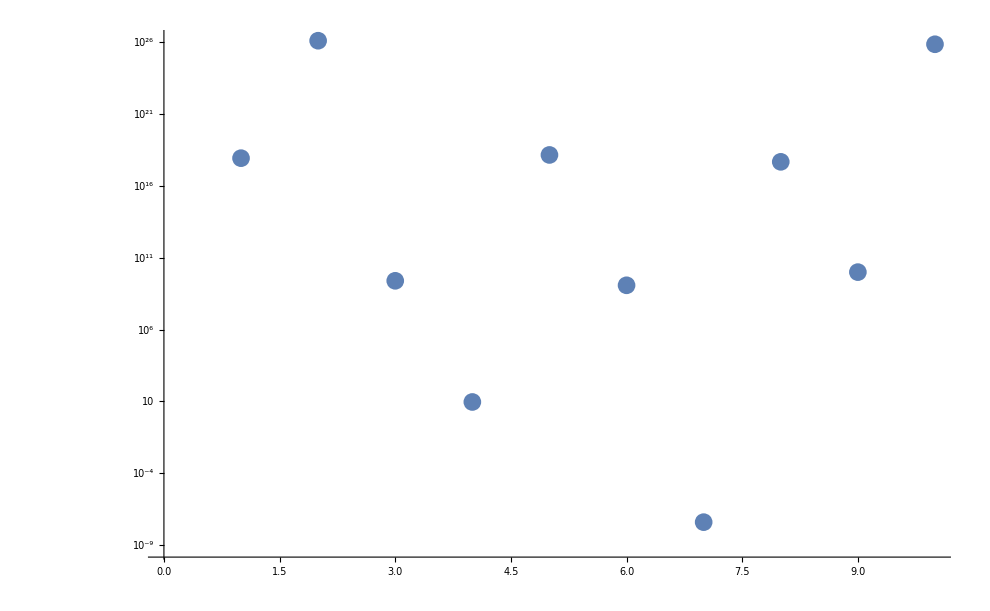

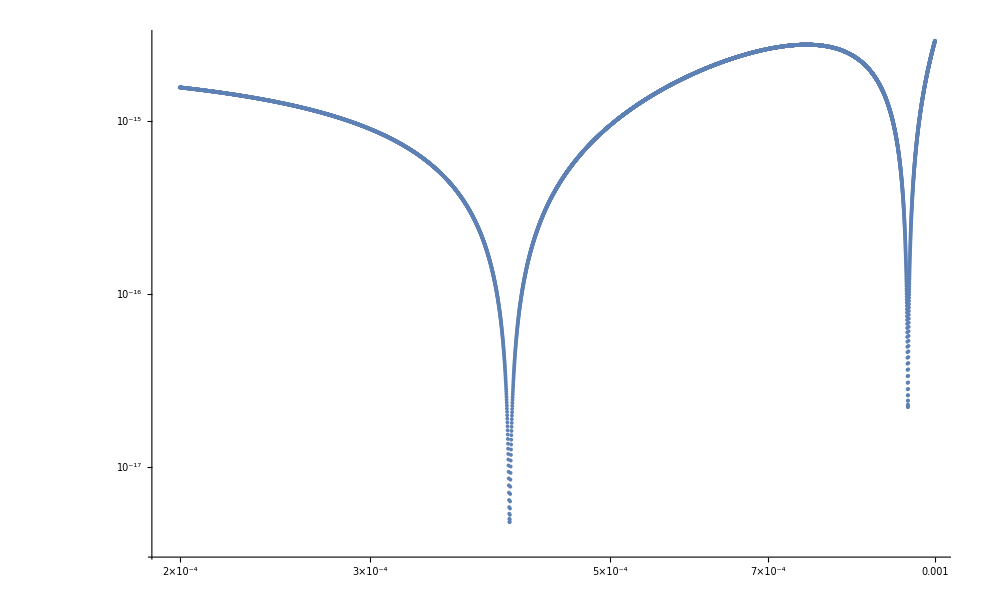

```mathematica
ListLogPlot[Abs[intList]]
ListLogLogPlot[Transpose[{ωSpec/(2*Pi), Abs[spec]}]]
```

```mathematica
Abs[M*u*(4*Pi^2*freqList^2-(2*Pi*400*10^-6)^2+I*(2*Pi*400*10^-6)*2*Pi*freqList/qList)/(4 Pi I intList)]
```

{1.10459×10^-7,3.71591×10^-17,34.6656,4.04698×10^10,3.09227×10^-7,191.305,1.9588×10^19,2.21751×10^-6,104.891,1.49388×10^-14}

```mathematica
ωSpec[[1]]/2*Pi
```

π^2/10000